```mathematica
(* mathematica*)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B]
```

```mathematica
Factor[-1-x-5 x^2+x^3]
```

-1-x-5 x^2+x^3

```mathematica
NSolve[-1-x-5 x^2+x^3==0,x]
```

{{x→-0.113936-0.422257 ⅈ},{x→-0.113936+0.422257 ⅈ},{x→5.22787}}

```mathematica
r[i_]:=x/.NSolve[-1-x-5 x^2+x^3==0,x][[i]]
```

```mathematica
s[1]=N[{{r[3],13.5},{0,1/r[1]}}]/Sqrt[Det[N[{{r[3],13.5},{0,1/r[1]}}]]]
s[2]=N[{{1,0},{13.5*I/(r[3]^2-1),1}}]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{0.91946-1.20044 ⅈ,2.37433-3.0999 ⅈ},{0.+0. ⅈ,0.402134+0.525021 ⅈ}}

{{1.,0.},{0.+0.512711 ⅈ,1.}}

{{0.402134+0.525021 ⅈ,-2.37433+3.0999 ⅈ},{0.+0. ⅈ,0.91946-1.20044 ⅈ}}

{{1.+0. ⅈ,0.+0. ⅈ},{0.-0.512711 ⅈ,1.+0. ⅈ}}

```mathematica
qf=N[rotate[Pi/4]];qfi=Inverse[qf]
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
```

{{0.707107,0.707107},{-0.707107,0.707107}}

```mathematica
{a,b,A,B}=Table[N[qf.s[i].qfi],{i,4}]
```

{{{-0.52637+1.21224 ⅈ,1.44583-2.41268 ⅈ},{-0.928503+0.687223 ⅈ,1.84796-1.88766 ⅈ}},{{1.-0.256355 ⅈ,0.-0.256355 ⅈ},{0.+0.256355 ⅈ,1.+0.256355 ⅈ}},{{1.84796-1.88766 ⅈ,-1.44583+2.41268 ⅈ},{0.928503-0.687223 ⅈ,-0.52637+1.21224 ⅈ}},{{1.+0.256355 ⅈ,0.+0.256355 ⅈ},{0.-0.256355 ⅈ,1.-0.256355 ⅈ}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

1.+5.55112×10^-16 ⅈ

1.32159-0.675415 ⅈ

1.+0. ⅈ

2.+0. ⅈ

1.+7.21645×10^-16 ⅈ

1.32159-0.675415 ⅈ

1.+0. ⅈ

2.+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],11];
ll=Length[aa1]
Last[aa1]
aa=aa1;
```

708588

{4.51994,0.514014}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-2,6},{-8/2,8/2}},Axes->False];
```

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[12*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

8

54

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-2,6},{-8/2,8/2}},Background->Black];
```

```mathematica
(* end limit set*)
```

```mathematica
(*Perpendicular Hermetian inversion conformal map: z*Conjugate[z]/Abs[z]^2=1*)
```

```mathematica
bb=Delete[Reverse[Union[Table[{aa[[i,1]],-aa[[i,2]]}/(aa[[i,1]]^2+aa[[i,2]]^2),{i,Length[aa]}]]],1];
```

```mathematica
g1=ListPlot[bb,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-20,20},{-20,20}}/12];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g5=Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-20,20},{-20,20}}/12,Background->Black];
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]]]];
```

```mathematica
ListPlot[bb1,PlotStyle->{{Yellow,PointSize[0.001]},{Orange,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->{-50,50}/10];
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];

g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->2],RasterSize->2000,ImageSize->2000];
```

```mathematica
cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False,ViewPoint->{2.1,2.1,2.1}],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_2group_Bombieri_10th_minimal_Pisot_Linear_cubic_Quasiconformal45_limitset_11.jpg",GraphicsGrid[{{g0,g2},{g1,g5},{g3,g4}},ImageSize->6000]]
```

Nylander_2group_Bombieri_10th_minimal_Pisot_Linear_cubic_Quasiconformal45_limitset_11.jpg

```mathematica
(*end*)
```

```mathematica
(*mathematica*)
```

```mathematica
(*Minimal Pisot linear  10-th cubic polynomial factor 8 group*)
```

```mathematica
p1=-1-x-5 x^2+x^3;
p2=1-x+5 x^2+x^3;
p3=-1+5 x+x^2+x^3;
p4=-1+5 x-x^2+x^3;
```

```mathematica
NSolve[p1==0,x]
```

{{x→-0.113936-0.422257 ⅈ},{x→-0.113936+0.422257 ⅈ},{x→5.22787}}

```mathematica
f={x+1,p1,x-1,p2,x+1,p3,x-1,p4}
```

{1+x,-1-x-5 x^2+x^3,-1+x,1-x+5 x^2+x^3,1+x,-1+5 x+x^2+x^3,-1+x,-1+5 x-x^2+x^3}

```mathematica
(* polynomial recursion in 8 factors*)
```

```mathematica
Clear[p,n,x]
```

```mathematica
p[1,x]=1
```

1

```mathematica
p[n_,x_]:=p[n,x]=p[n-1,x]*f[[1+Mod[n,8]]]
```

```mathematica
(*Polynomials*)
```

```mathematica
px=Table[Expand[FullSimplify[ExpandAll[p[i,x]]]],{i,11}]
```

{1,-1+x,-1+2 x-6 x^2+4 x^3+x^4,-1+x-4 x^2-2 x^3+5 x^4+x^5,1-6 x+8 x^2-18 x^3-18 x^4+18 x^5+8 x^6+6 x^7+x^8,-1+7 x-14 x^2+26 x^3-36 x^5+10 x^6+2 x^7+5 x^8+x^9,1-12 x+50 x^2-104 x^3+151 x^4-4 x^5-164 x^6+84 x^7-41 x^8+32 x^9+2 x^10+4 x^11+x^12,1-11 x+38 x^2-54 x^3+47 x^4+147 x^5-168 x^6-80 x^7+43 x^8-9 x^9+34 x^10+6 x^11+5 x^12+x^13,-1+10 x-32 x^2+72 x^3-194 x^4+114 x^5-268 x^6-440 x^7+1024 x^8+198 x^9-320 x^10+48 x^11-190 x^12-2 x^13-20 x^14+x^16,1-11 x+42 x^2-104 x^3+266 x^4-308 x^5+382 x^6+172 x^7-1464 x^8+826 x^9+518 x^10-368 x^11+238 x^12-188 x^13+18 x^14-20 x^15-x^16+x^17,1-12 x+58 x^2-200 x^3+569 x^4-1052 x^5+1916 x^6-1484 x^7-34 x^8+3532 x^9-7456 x^10+1780 x^11+4022 x^12-1748 x^13+1028 x^14-740 x^15-79 x^16-80 x^17-26 x^18+4 x^19+x^20}

```mathematica
(* Coefficients triangle*)
```

```mathematica
v=Table[CoefficientList[p[i,x],x],{i,11}]
```

{{1},{-1,1},{-1,2,-6,4,1},{-1,1,-4,-2,5,1},{1,-6,8,-18,-18,18,8,6,1},{-1,7,-14,26,0,-36,10,2,5,1},{1,-12,50,-104,151,-4,-164,84,-41,32,2,4,1},{1,-11,38,-54,47,147,-168,-80,43,-9,34,6,5,1},{-1,10,-32,72,-194,114,-268,-440,1024,198,-320,48,-190,-2,-20,0,1},{1,-11,42,-104,266,-308,382,172,-1464,826,518,-368,238,-188,18,-20,-1,1},{1,-12,58,-200,569,-1052,1916,-1484,-34,3532,-7456,1780,4022,-1748,1028,-740,-79,-80,-26,4,1}}

```mathematica
Flatten[Abs[v]]
```

{1,1,1,1,2,6,4,1,1,1,4,2,5,1,1,6,8,18,18,18,8,6,1,1,7,14,26,0,36,10,2,5,1,1,12,50,104,151,4,164,84,41,32,2,4,1,1,11,38,54,47,147,168,80,43,9,34,6,5,1,1,10,32,72,194,114,268,440,1024,198,320,48,190,2,20,0,1,1,11,42,104,266,308,382,172,1464,826,518,368,238,188,18,20,1,1,1,12,58,200,569,1052,1916,1484,34,3532,7456,1780,4022,1748,1028,740,79,80,26,4,1}

```mathematica
(*row sums*)
```

```mathematica
rsa0=Table[Apply[Plus,v[[i]]],{i,Length[v]}]
```

{1,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*row (absolute value) sums*)
```

```mathematica
rsa=Table[Apply[Plus,Abs[v[[i]]]],{i,Length[v]}]
```

{1,2,14,14,84,102,650,644,2934,4928,25822}

```mathematica
TableForm[Table[CoefficientList[p[i,x],x],{i,11}]]
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 2 | -6 | 4 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 1 | -4 | -2 | 5 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -6 | 8 | -18 | -18 | 18 | 8 | 6 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 7 | -14 | 26 | 0 | -36 | 10 | 2 | 5 | 1 |  |  |  |  |  |  |  |  |  |  | 
1 | -12 | 50 | -104 | 151 | -4 | -164 | 84 | -41 | 32 | 2 | 4 | 1 |  |  |  |  |  |  |  | 
1 | -11 | 38 | -54 | 47 | 147 | -168 | -80 | 43 | -9 | 34 | 6 | 5 | 1 |  |  |  |  |  |  | 
-1 | 10 | -32 | 72 | -194 | 114 | -268 | -440 | 1024 | 198 | -320 | 48 | -190 | -2 | -20 | 0 | 1 |  |  |  | 
1 | -11 | 42 | -104 | 266 | -308 | 382 | 172 | -1464 | 826 | 518 | -368 | 238 | -188 | 18 | -20 | -1 | 1 |  |  | 
1 | -12 | 58 | -200 | 569 | -1052 | 1916 | -1484 | -34 | 3532 | -7456 | 1780 | 4022 | -1748 | 1028 | -740 | -79 | -80 | -26 | 4 | 1

```mathematica
(*Pictures*)
```

```mathematica
lvl=1024
```

1024

```mathematica
w=Table[CoefficientList[p[i,x],x],{i,lvl}];
```

```mathematica
ww=ParallelTable[Join[Mod[w[[i]],2],Table[0,{j,Length[w[[lvl]]]-Length[w[[i]]]}]],{i,Length[w]}];
```

```mathematica
Dimensions[ww]
```

{1024,2046}

```mathematica
g1=ListDensityPlot[ww,ColorFunction->"CMYKColors",ImageSize->2000];
```

```mathematica
Export["Minimal_Pisot_linear_10th_cubic_triangle_recursive_Polynomial_1024_2046_g1.jpg",g1]
```

Minimal_Pisot_linear_10th_cubic_triangle_recursive_Polynomial_1024_2046_g1.jpg

```mathematica
Clear[p,q]
```

```mathematica
p[x_]=px[[9]]
```

-1+10 x-32 x^2+72 x^3-194 x^4+114 x^5-268 x^6-440 x^7+1024 x^8+198 x^9-320 x^10+48 x^11-190 x^12-2 x^13-20 x^14+x^16

```mathematica
(*Polynomial expansion*)
```

```mathematica
q[x_]=ExpandAll[x^16*p[1/x]]
a=Abs[Table[-SeriesCoefficient[Series[1/p[x],{x,0,50}],m],{m,0,50,2}]]
```

1-20 x^2-2 x^3-190 x^4+48 x^5-320 x^6+198 x^7+1024 x^8-440 x^9-268 x^10+114 x^11-194 x^12+72 x^13-32 x^14+10 x^15-x^16

{1,68,2670,92804,2996372,92661340,2784337738,81987190396,2378500073385,68227136577368,1940024669098100,54783911365042008,1538481873281048208,43011283416194715592,1198061035175739026348,33270796298843486691592,921637426583614716565497,25477187591637497018957756,703048972872888046726509714,19372430876352322412997419004,533147898558935302214593394164,14657499035340275186548129346244,402615360976909533459409621413542,11050895403177386198962904045434148,303130956140444450104904224106186737,8310556448780368646077270845396589552}

```mathematica
Table[N[a[[i+1]]/a[[i]]],{i,Length[a]-1}]
```

{68.,39.2647,34.7581,32.2871,30.9245,30.0485,29.4458,29.0106,28.6849,28.4348,28.2388,28.0827,27.957,27.8546,27.7705,27.7011,27.6434,27.5952,27.5549,27.521,27.4924,27.4682,27.4478,27.4304,27.4157}

```mathematica
x/.NSolve[p[x]==0,x]
```

{-5.22787,-1.,-1.,-0.595641-2.20751 ⅈ,-0.595641+2.20751 ⅈ,-0.113936+0.422257 ⅈ,-0.113936-0.422257 ⅈ,0.113936+0.422257 ⅈ,0.113936-0.422257 ⅈ,0.191282,0.206783,0.396608+2.16303 ⅈ,0.396608-2.16303 ⅈ,1.,1.,5.22787}

```mathematica
r[x_]=p[x]/.x->x^(1/2)
```

-1+10 √x-32 x+72 x^(3/2)-194 x^2+114 x^(5/2)-268 x^3-440 x^(7/2)+1024 x^4+198 x^(9/2)-320 x^5+48 x^(11/2)-190 x^6-2 x^(13/2)-20 x^7+x^8

```mathematica
x/.NSolve[r[x]==0,x]
```

{1.,1.,-0.16532-0.0962203 ⅈ,-0.16532+0.0962203 ⅈ,0.0427594,0.036589}

```mathematica
qr[x_]=ExpandAll[x^8*r[1/x]]
ar=Abs[Table[-SeriesCoefficient[Series[1/qr[x],{x,0,50}],m],{m,0,50}]]
```

1+10/(1/x)^(15/2)+72/(1/x)^(13/2)+114/(1/x)^(11/2)-440/(1/x)^(9/2)+198/(1/x)^(7/2)+48/(1/x)^(5/2)-2/(1/x)^(3/2)-20 x-190 x^2-320 x^3+1024 x^4-268 x^5-194 x^6-32 x^7-x^8

{1,20,590,15924,435924,11912780,325577898,8898335756,243196632233,6646722380088,181659162433716,4964861101693560,135692829018035472,3708571791384513512,101357638697402247660,2770169083745577486824,75710492581302746390777,2069216179087633006325228,56553001437678280432956338,1545629694921711210211649100,42243047992004239591127607476,1154529516039848166047170430804,31554029994698859163755622887238,862391818549219828293440147539732,23569719900297265041751845983792625,644175517704963832742025100062136496,17605728848955248092911400998355075528,481175828301036670254336354218590882608,13150843099286292293560994071591240152512,359420951864288177206693294908816035845904,9823204464057658451890808661849736489210424,268474459939434658088221362947383253406877968,7337578679493118982626118176354174074747222673,200540717690233182112151393857603867698813697028,5480906060211673422529810275262077166747498590070,149796667663606774166296863168658739667722324216484,4094038722176978196474895793665863536079736745117236,111892696413811083945741387686106692532218352076784028,3058098948340155677077457828240764969204636976932243010,83579799911630680014799508740744507911207175608345552220,2284289380845503572577229597856309840727953479299036124121,62431089580981612735395472178668082790953484085589469575784,1706281602914024706688887614712620889720087089408330527696700,46633767374288347098791102076452997014999961616152703294176808,1274530684621592575640295140068789286096055686182951330014845456,34833738672754508690883777588160233018342065038145156965207029112,952028354093340356181723442243021572085634056391045133550366973156,26019543739259601787700127233995092218465897795793853110756286433656,711130769885522065982229830075642861796188665147240976156952351120585,19435658708916525537965688280590555992644501030798168212778782885650012,531188981613455147720701352173859793320539854339379714541565872951644570}

```mathematica
Table[N[ar[[i+1]]/ar[[i]]],{i,Length[ar]-1}]
```

{20.,29.5,26.9898,27.3753,27.3277,27.3301,27.3309,27.3306,27.3307,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306,27.3306}

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(*10 Minimal Pisot cubic polynomials*)
```

```mathematica
(* *)
```

```mathematica
q={x^3-1,x^3-x-1,1-2 x-x^2+x^3,-1-4 x-x^2+x^3,1-x-2 x^2+x^3,-1-(3) x^2+x^3,-1-5 x-2 x^2+x^3,1-4 x-3 x^2+x^3,-1+3 x-5 x^2+x^3,1-4* x-4* x^2+x^3,-1-x-5 x^2+x^3}
```

{-1+x^3,-1-x+x^3,1-2 x-x^2+x^3,-1-4 x-x^2+x^3,1-x-2 x^2+x^3,-1-3 x^2+x^3,-1-5 x-2 x^2+x^3,1-4 x-3 x^2+x^3,-1+3 x-5 x^2+x^3,1-4 x-4 x^2+x^3,-1-x-5 x^2+x^3}

```mathematica
(*solving for the basis matrix for 9 of the  cubic polynomial*)
```

```mathematica
Clear[m,p,x,a,b,x,q,w1,w2]
```

```mathematica
m={{a,0,1},{b,0,1},{0,c,0}}
```

{{a,0,1},{b,0,1},{0,c,0}}

```mathematica
p[x_]=CharacteristicPolynomial[m,x]
```

-a c+b c+c x+a x^2-x^3

```mathematica
w1=CoefficientList[p[x],x]
```

{-a c+b c,c,a,-1}

```mathematica
q={x^3-1,x^3-x-1,1-2 x-x^2+x^3,-1-4 x-x^2+x^3,1-x-2 x^2+x^3,-1-(3) x^2+x^3,-1-5 x-2 x^2+x^3,1-4 x-3 x^2+x^3,-1+3 x-5 x^2+x^3,1-4* x-4* x^2+x^3,-1-x-5 x^2+x^3}
```

{-1+x^3,-1-x+x^3,1-2 x-x^2+x^3,-1-4 x-x^2+x^3,1-x-2 x^2+x^3,-1-3 x^2+x^3,-1-5 x-2 x^2+x^3,1-4 x-3 x^2+x^3,-1+3 x-5 x^2+x^3,1-4 x-4 x^2+x^3,-1-x-5 x^2+x^3}

```mathematica
w2[j_]:=-CoefficientList[q[[j]],x]
```

```mathematica
Table[{q[[j]],m/.NSolve[Table[w1[[i]]-w2[j][[i]]==0,{i,3}],{a,b,c}]},{j,2,Length[q]}]
```

{{-1-x+x^3,{{{0.,0,1},{1.,0,1},{0,1.,0}}}},{1-2 x-x^2+x^3,{{{1.,0,1},{0.5,0,1},{0,2.,0}}}},{-1-4 x-x^2+x^3,{{{1.,0,1},{1.25,0,1},{0,4.,0}}}},{1-x-2 x^2+x^3,{{{2.,0,1},{1.,0,1},{0,1.,0}}}},{-1-3 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1-5 x-2 x^2+x^3,{{{2.,0,1},{2.2,0,1},{0,5.,0}}}},{1-4 x-3 x^2+x^3,{{{3.,0,1},{2.75,0,1},{0,4.,0}}}},{-1+3 x-5 x^2+x^3,{{{5.,0,1},{4.66667,0,1},{0,-3.,0}}}},{1-4 x-4 x^2+x^3,{{{4.,0,1},{3.75,0,1},{0,4.,0}}}},{-1-x-5 x^2+x^3,{{{5.,0,1},{6.,0,1},{0,1.,0}}}}}

```mathematica
(* two generator 3x3 extended 10th Minimal Pisot Polynomial group*)
s[1]={{5,0,1},{6,0,1},{0,1,0}}
s[2]=-s[1]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{5,0,1},{6,0,1},{0,1,0}}

{{-5,0,-1},{-6,0,-1},{0,-1,0}}

{{-1,1,0},{0,0,1},{6,-5,0}}

{{1,-1,0},{0,0,-1},{-6,5,0}}

```mathematica
p[1]=-CharacteristicPolynomial[s[1],x]
```

-1-x-5 x^2+x^3

```mathematica
p[2]=-CharacteristicPolynomial[s[2],x]
```

1-x+5 x^2+x^3

```mathematica
p[3]=-CharacteristicPolynomial[s[3],x]
```

-1+5 x+x^2+x^3

```mathematica
p[4]=-CharacteristicPolynomial[s[4],x]
```

1+5 x-x^2+x^3

```mathematica
Table[Det[s[i]],{i,4}]
```

{1,-1,1,-1}

```mathematica
Table[x/.NSolve[p[i]==0,x],{i,4}]
```

{{-0.113936-0.422257 ⅈ,-0.113936+0.422257 ⅈ,5.22787},{-5.22787,0.113936-0.422257 ⅈ,0.113936+0.422257 ⅈ},{-0.595641-2.20751 ⅈ,-0.595641+2.20751 ⅈ,0.191282},{-0.191282,0.595641-2.20751 ⅈ,0.595641+2.20751 ⅈ}}

```mathematica
Table[Tr[s[i]],{i,4}]
```

{5,-5,-1,1}

```mathematica
(* Casimir invariant*)
```

```mathematica
Sum[s[i].s[i],{i,4}]
```

{{52,0,12},{72,-8,12},{0,12,-8}}

```mathematica
(*Killing vectors*)
```

```mathematica
kl=Table[s[i].{1,1,1},{i,4}]
```

{{6,7,1},{-6,-7,-1},{0,1,1},{0,-1,-1}}

```mathematica
(*Pseudo-Cartan matrix*)
```

```mathematica
kt=kl.Transpose[kl]
```

{{86,-86,8,-8},{-86,86,-8,8},{8,-8,2,-2},{-8,8,-2,2}}

```mathematica
eg0=N[Eigenvalues[kt]]//Chop
```

{173.51,2.48977,0,0}

```mathematica
Apply[Plus,eg0]
```

176.

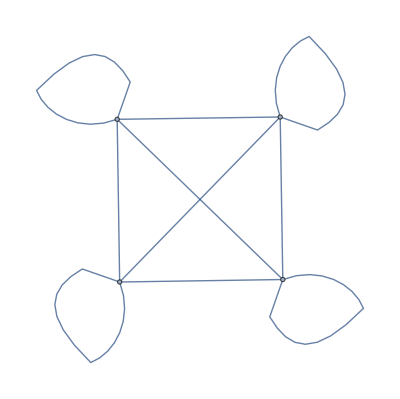

```mathematica
WeightedAdjacencyGraph[kt]
```

```mathematica
Transpose[kl].kl
```

{{72,84,12},{84,100,16},{12,16,4}}

```mathematica
(* Cartan matrix*)
```

```mathematica
ct=Table[2*kl[[i]].kl[[j]]/(kl[[i]].kl[[i]]),{i,4},{j,4}]
```

{{2,-2,8/43,-8/43},{-2,2,-8/43,8/43},{8,-8,2,-2},{-8,8,-2,2}}

```mathematica
MatrixForm[ct]
```

(2 | -2 | 8/43 | -8/43
-2 | 2 | -8/43 | 8/43
8 | -8 | 2 | -2
-8 | 8 | -2 | 2)

```mathematica
eg=N[Eigenvalues[ct]]//Chop
```

{6.43998,1.56002,0,0}

```mathematica
Apply[Plus,eg]
```

8.

```mathematica
WeightedAdjacencyGraph[ct]
```

-Graphics-

```mathematica
(*end*)
```